# Mathematica Assignment Olek Yardas Mat 220 FA’17 Chris French

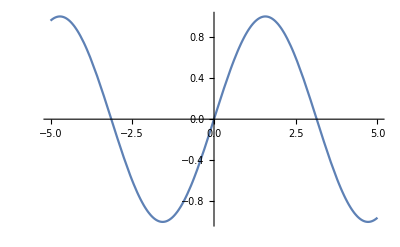
1
Plot[Sin[x], {x, -5, 5}]
-Graphics-

2

```mathematica
DSolve[{y'[x]==1+3*y[x]^(1/2), y[0]==1}, y, x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},1/9 (1+ProductLog[2 ⅇ^(2-(9 x)/2)])^2]},{y→Function[{x},1/9 (1+ProductLog[-ⅇ^(-(9 x)/2+9 ⅈ (π-ⅈ Log[2^(1/9) ⅇ^(2/9)]))])^2]}}

```mathematica
f[x_]:=1/9 (1+ProductLog[2 ⅇ^(2-(9 x)/2)])^2
```

3

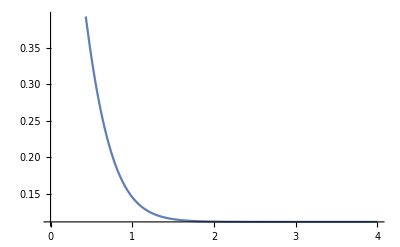

```mathematica
Plot[f[x], {x, 0, 4}]
```

4

```mathematica
m={{2,5,4},{3,7,1},{2,9,8}}
Inverse[m]
```

{{2,5,4},{3,7,1},{2,9,8}}

{{47/36,-1/9,-23/36},{-11/18,2/9,5/18},{13/36,-2/9,-1/36}}

5

```mathematica
Eigenvalues[m]
```

{7+√37,3,7-√37}

```mathematica
Eigenvectors[m]
```

{{-(-28+√37)/(27+2 √37),-(1-3 √37)/(27+2 √37),1},{11,-13,19},{-(28+√37)/(-27+2 √37),-(-1-3 √37)/(-27+2 √37),1}}